```mathematica
Clear["Global`*"];
dim=3/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
Hmuti[ϕ1_,ϕ2_,ϕ3_]:=({{0, (√3)/2 ⅇ^(-ⅈ ϕ1), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ1), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}});
Iplus5half2=Ix3half2+I*Iy3half2;
Iminus5half2=Ix3half2-I*Iy3half2;
UHmuti[ϕ1_,ϕ2_,ϕ3_,t_]:=N[MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3]*t] ]
IniPhi={{1},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^3},{1/4 √3 ⅇ^(ⅈ ϕ) Csc[θ/2] Sin[θ]^2},{1/2 √3 ⅇ^(2 ⅈ ϕ) Sin[θ/2] Sin[θ]},{ⅇ^(3 ⅈ ϕ) Sin[θ/2]^3}}

StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,θ_,ϕ_]:=N[UHmuti[ϕ1,ϕ2,ϕ3,t].StateθϕInitial[θ,ϕ]]
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
Chop[N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]]
]
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
If[Chop[N[First[Flatten[yVal]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],Chop[N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]]
]

In1[state_]:=Chop[N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]]
In2[state_]:=Chop[N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]]
In1n2plusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]]
In1n2minusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]]
In1n2n2n1[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]]
ξSqure[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]
```

```mathematica
N[MatrixExp[-I*Iz3half2.Iz3half2*0.534] ].StateθϕInitial[Pi/2,Pi/2]
```

{{0.127618-0.329717 ⅈ},{0.0815091+0.606924 ⅈ},{-0.606924+0.0815091 ⅈ},{-0.329717-0.127618 ⅈ}}

```mathematica
StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,0.534,Pi/2,Pi/2]
```

{{0.0616185+0.0930654 ⅈ},{0.321502+0.619821 ⅈ},{-0.619821+0.321502 ⅈ},{0.0930654-0.0616185 ⅈ}}

```mathematica
MatrixExp[-I*Iz3half2.Iz3half2*t].StateθϕInitial[Pi/2,Pi/2]
```

{{ⅇ^(-(9 ⅈ t)/4)/(2 √2)},{1/2 ⅈ √(3/2) ⅇ^(-(ⅈ t)/4)},{-1/2 √(3/2) ⅇ^(-(ⅈ t)/4)},{-(ⅈ ⅇ^(-(9 ⅈ t)/4))/(2 √2)}}

```mathematica
StateθϕInitial[Pi/2,Pi/2]
```

{{1/(2 √2)},{1/2 ⅈ √(3/2)},{-(√(3/2))/2},{-ⅈ/(2 √2)}}

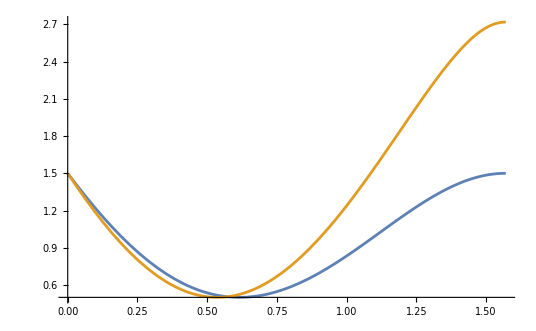

```mathematica
Plot[{ξSqure[N[MatrixExp[-I*Iz3half2.Iz3half2*t] ].StateθϕInitial[Pi/2,Pi/2]],ξSqure[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]]},{t,0,Pi/2}]
```

```mathematica
ss=N[MatrixExp[-I*Iz3half2.Iz3half2*t] ].StateθϕInitial[Pi/2,Pi/2];
ss2=StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2];
```

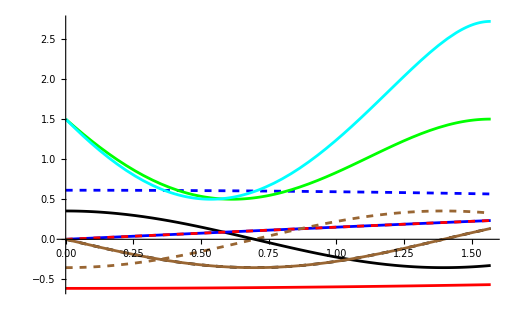

```mathematica
Plot[{Re[ss[[1]]],Im[ss[[1]]],Re[ss[[2]]],Im[ss[[2]]],Re[ss[[3]]],Im[ss[[3]]],Re[ss[[4]]],Im[ss[[4]]],ξSqure[N[MatrixExp[-I*Iz3half2.Iz3half2*t] ].StateθϕInitial[Pi/2,Pi/2]],ξSqure[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]]},{t,0,Pi/2},PlotStyle->{Black,{Black,Dashed},Blue,{Blue,Dashed},Red,{Red,Dashed},Brown,{Brown,Dashed},Green,Cyan}]
```

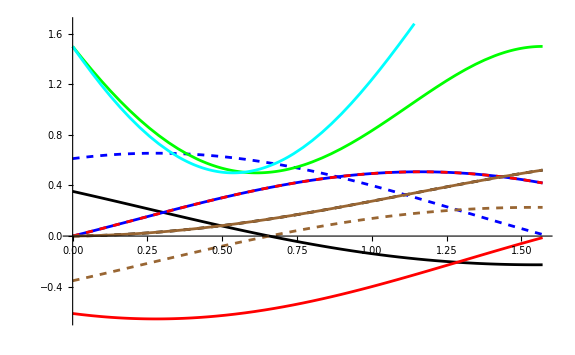

```mathematica
Plot[{Re[ss2[[1]]],Im[ss2[[1]]],Re[ss2[[2]]],Im[ss2[[2]]],Re[ss2[[3]]],Im[ss2[[3]]],Re[ss2[[4]]],Im[ss2[[4]]],ξSqure[N[MatrixExp[-I*Iz3half2.Iz3half2*t] ].StateθϕInitial[Pi/2,Pi/2]],ξSqure[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]]},{t,0,Pi/2},PlotStyle->{Black,{Black,Dashed},Blue,{Blue,Dashed},Red,{Red,Dashed},Brown,{Brown,Dashed},Green,Cyan}]
```

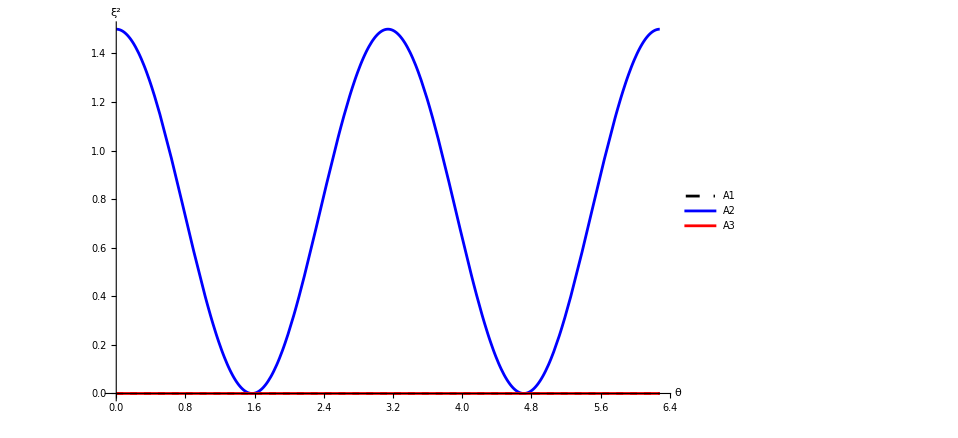

```mathematica
Ix3halfAve=Plot[{Chop[ConjugateTranspose[ss].Ix3half2.ss],Chop[ConjugateTranspose[ss].Iy3half2.ss],Chop[ConjugateTranspose[ss].Iz3half2.ss]},{t,0,2Pi},PlotStyle->{{Black,Dashed},Blue,Red,Green},AxesLabel->{"θ","ξ^2"},AxesStyle->Directive[Thick,Black],PlotLegends->{"A1","A2","A3","A4"}]
```

```mathematica
ss[[1]]
ss[[2]]
ss[[3]]
ss[[4]]
```

{(0.+0. ⅈ)+2.71828^((0.-2.25 ⅈ) t)/(2 √2)}

{(0.+0. ⅈ)+1/2 ⅈ √(3/2) 2.71828^((0.-0.25 ⅈ) t)}

{(0.+0. ⅈ)-1/2 √(3/2) 2.71828^((0.-0.25 ⅈ) t)}

{(0.+0. ⅈ)-(ⅈ 2.71828^((0.-2.25 ⅈ) t))/(2 √2)}

```mathematica
Norm[(N[MatrixExp[-I*Iz3half2.Iz3half2*1] ].StateθϕInitial[Pi/2,Pi/2])]
```

1.

```mathematica
TableIy=Table[0,{i,1,200}];
Do[
TableIy[[i]]=Chop[ConjugateTranspose[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,Pi/200*i,Pi/2,Pi/2]].Iy3half2.StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,Pi/200*i,Pi/2,Pi/2]];

,{i,1,200}]
```

```mathematica
Flatten[TableIy]
```

{1.49953,1.49811,1.49575,1.49245,1.48821,1.48303,1.47693,1.46991,1.46197,1.45312,1.44338,1.43274,1.42122,1.40884,1.39561,1.38153,1.36662,1.3509,1.33438,1.31707,1.29901,1.2802,1.26065,1.2404,1.21946,1.19786,1.1756,1.15272,1.12924,1.10518,1.08056,1.05541,1.02976,1.00362,0.977028,0.950007,0.922583,0.894785,0.866638,0.838171,0.809412,0.780389,0.751131,0.721667,0.692026,0.662237,0.63233,0.602333,0.572277,0.542192,0.512107,0.482051,0.452054,0.422147,0.392358,0.362717,0.333253,0.303995,0.274972,0.246213,0.217746,0.189599,0.161801,0.134377,0.107356,0.0807645,0.054628,0.0289728,0.00382403,-0.0207934,-0.0448553,-0.0683378,-0.0912178,-0.113473,-0.135081,-0.15602,-0.17627,-0.195812,-0.214625,-0.232691,-0.249992,-0.266512,-0.282234,-0.297142,-0.311221,-0.324459,-0.336841,-0.348355,-0.358991,-0.368738,-0.377585,-0.385525,-0.392549,-0.398651,-0.403824,-0.408063,-0.411365,-0.413726,-0.415143,-0.415616,-0.415143,-0.413726,-0.411365,-0.408063,-0.403824,-0.398651,-0.392549,-0.385525,-0.377585,-0.368738,-0.358991,-0.348355,-0.336841,-0.324459,-0.311221,-0.297142,-0.282234,-0.266512,-0.249992,-0.232691,-0.214625,-0.195812,-0.17627,-0.15602,-0.135081,-0.113473,-0.0912178,-0.0683378,-0.0448553,-0.0207934,0.00382403,0.0289728,0.054628,0.0807645,0.107356,0.134377,0.161801,0.189599,0.217746,0.246213,0.274972,0.303995,0.333253,0.362717,0.392358,0.422147,0.452054,0.482051,0.512107,0.542192,0.572277,0.602333,0.63233,0.662237,0.692026,0.721667,0.751131,0.780389,0.809412,0.838171,0.866638,0.894785,0.922583,0.950007,0.977028,1.00362,1.02976,1.05541,1.08056,1.10518,1.12924,1.15272,1.1756,1.19786,1.21946,1.2404,1.26065,1.2802,1.29901,1.31707,1.33438,1.3509,1.36662,1.38153,1.39561,1.40884,1.42122,1.43274,1.44338,1.45312,1.46197,1.46991,1.47693,1.48303,1.48821,1.49245,1.49575,1.49811,1.49953,1.5}

```mathematica
{{3.2010852203572133,1.5707963031116705,-0.05949256001795611},{2.456198367342221,-1.2977183328584863,0.5624148170023302},{-0.4109857882614181,1.5622697396088778,-2.181721281209474},{3.519591081486965,1.5891289268521644,-0.3910899766575895}}
```

```mathematica
N[Pi/2]
```

1.5708

```mathematica
NumberForm[1.5707963267948966,16]
```

1.570796326794897

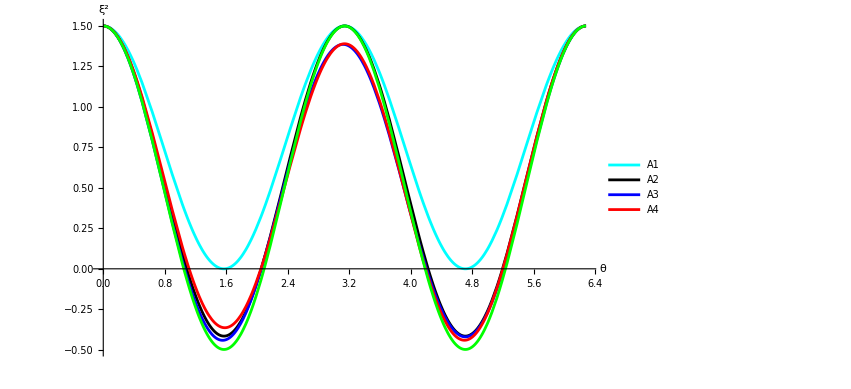

```mathematica
Ix3halfAve=Plot[{Chop[ConjugateTranspose[ss].Iy3half2.ss],Chop[ConjugateTranspose[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]].Iy3half2.StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]],ConjugateTranspose[StateEvo[2.456198367342221,-1.2977183328584863,0.5624148170023302,t,Pi/2,Pi/2]].Iy3half2.StateEvo[2.456198367342221,-1.2977183328584863,0.5624148170023302,t,Pi/2,Pi/2],Chop[ConjugateTranspose[StateEvo[-0.4109857882614181,1.5622697396088778,-2.181721281209474,t,Pi/2,Pi/2]].Iy3half2.StateEvo[-0.4109857882614181,1.5622697396088778,-2.181721281209474,t,Pi/2,Pi/2]],Chop[ConjugateTranspose[StateEvo[3.519591081486965,1.5891289268521644,-0.3910899766575895,t,Pi/2,Pi/2]].Iy3half2.StateEvo[3.519591081486965,1.5891289268521644,-0.3910899766575895,t,Pi/2,Pi/2]]},{t,0,2Pi},PlotStyle->{Cyan,Black,Blue,Red,Green},AxesLabel->{"θ","ξ^2"},AxesStyle->Directive[Thick,Black],PlotLegends->{"A1","A2","A3","A4"}]
```

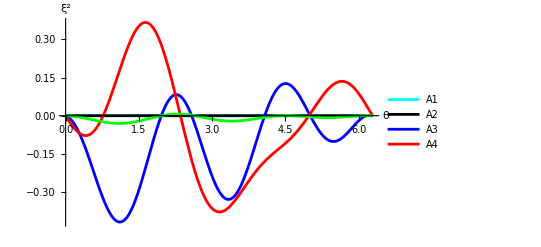

```mathematica
Iy3halfAve=Plot[{Chop[ConjugateTranspose[ss].Ix3half2.ss],Chop[ConjugateTranspose[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]].Ix3half2.StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]],ConjugateTranspose[StateEvo[2.456198367342221,-1.2977183328584863,0.5624148170023302,t,Pi/2,Pi/2]].Ix3half2.StateEvo[2.456198367342221,-1.2977183328584863,0.5624148170023302,t,Pi/2,Pi/2],Chop[ConjugateTranspose[StateEvo[-0.4109857882614181,1.5622697396088778,-2.181721281209474,t,Pi/2,Pi/2]].Ix3half2.StateEvo[-0.4109857882614181,1.5622697396088778,-2.181721281209474,t,Pi/2,Pi/2]],Chop[ConjugateTranspose[StateEvo[3.519591081486965,1.5891289268521644,-0.3910899766575895,t,Pi/2,Pi/2]].Ix3half2.StateEvo[3.519591081486965,1.5891289268521644,-0.3910899766575895,t,Pi/2,Pi/2]]},{t,0,2Pi},PlotStyle->{Cyan,Black,Blue,Red,Green},AxesLabel->{"θ","ξ^2"},AxesStyle->Directive[Thick,Black],PlotLegends->{"A1","A2","A3","A4"},PlotRange->All]
```

```mathematica
Iz3halfAve=Plot[Chop[ConjugateTranspose[ss].Iz3half2.ss],{Chop[ConjugateTranspose[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]].Iz3half2.StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]],ConjugateTranspose[StateEvo[2.456198367342221,-1.2977183328584863,0.5624148170023302,t,Pi/2,Pi/2]].Iz3half2.StateEvo[2.456198367342221,-1.2977183328584863,0.5624148170023302,t,Pi/2,Pi/2],Chop[ConjugateTranspose[StateEvo[-0.4109857882614181,1.5622697396088778,-2.181721281209474,t,Pi/2,Pi/2]].Iz3half2.StateEvo[-0.4109857882614181,1.5622697396088778,-2.181721281209474,t,Pi/2,Pi/2]],Chop[ConjugateTranspose[StateEvo[3.519591081486965,1.5891289268521644,-0.3910899766575895,t,Pi/2,Pi/2]].Iz3half2.StateEvo[3.519591081486965,1.5891289268521644,-0.3910899766575895,t,Pi/2,Pi/2]]},{t,0,2Pi},PlotStyle->{Black,Blue,Red,Green},AxesLabel->{"θ","ξ^2"},AxesStyle->Directive[Thick,Black],PlotLegends->{"A1","A2","A3","A4"}]
```

Plot::nonopt: Plot[Chop[ConjugateTranspose[ss].Iz3half2.ss],{Chop[ConjugateTranspose[StateEvo[3.20109,1.5708,-0.0594926,t,π Power[«2»],π Power[«2»]]].Iz3half2.StateEvo[3.20109,1.5708,-0.0594926,t,π/2,π/2]],ConjugateTranspose[StateEvo[2.4562,-1.29772,0.562415,t,π/2,π/2]].Iz3half2.StateEvo[2.4562,-1.29772,0.562415,t,π/2,π/2],Chop[ConjugateTranspose[StateEvo[-0.410986,1.56227,-2.18172,t,π Power[«2»],π Power[«2»]]].Iz3half2.StateEvo[-0.410986,1.56227,-2.18172,t,π/2,π/2]],Chop[ConjugateTranspose[StateEvo[3.51959,1.58913,-0.39109,t,π Power[«2»],π Power[«2»]]].Iz3half2.StateEvo[3.51959,1.58913,-0.39109,t,π/2,π/2]]},{t,0,2 π},PlotStyle→{Black,Blue,Red,Green},AxesLabel→{θ,ξ^2},AxesStyle→Directive[Thick,Black],PlotLegends→{A1,A2,A3,A4}] 中位置 2 外应该是选项（而不是 {t,0,2 π}）. 选项必须是一个规则或者规则列表.

Plot[Chop[ConjugateTranspose[ss].Iz3half2.ss],{Chop[ConjugateTranspose[StateEvo[3.20109,1.5708,-0.0594926,t,π/2,π/2]].Iz3half2.StateEvo[3.20109,1.5708,-0.0594926,t,π/2,π/2]],ConjugateTranspose[StateEvo[2.4562,-1.29772,0.562415,t,π/2,π/2]].Iz3half2.StateEvo[2.4562,-1.29772,0.562415,t,π/2,π/2],Chop[ConjugateTranspose[StateEvo[-0.410986,1.56227,-2.18172,t,π/2,π/2]].Iz3half2.StateEvo[-0.410986,1.56227,-2.18172,t,π/2,π/2]],Chop[ConjugateTranspose[StateEvo[3.51959,1.58913,-0.39109,t,π/2,π/2]].Iz3half2.StateEvo[3.51959,1.58913,-0.39109,t,π/2,π/2]]},{t,0,2 π},PlotStyle→{Black,Blue,Red,Green},AxesLabel→{θ,ξ^2},AxesStyle→Directive[Thick,Black],PlotLegends→{A1,A2,A3,A4}]

```mathematica
Export["D:\\desksave2\\Astro\\spin squeezing\\picture save\\Ix3halfAve.pdf",Ix3halfAve]
Export["D:\\desksave2\\Astro\\spin squeezing\\picture save\\Iy3halfAve.pdf",Iy3halfAve]
Export["D:\\desksave2\\Astro\\spin squeezing\\picture save\\Iz3halfAve.pdf",Iz3halfAve]
```

D:\desksave2\Astro\spin squeezing\picture save\Ix3halfAve.pdf

D:\desksave2\Astro\spin squeezing\picture save\Iy3halfAve.pdf

D:\desksave2\Astro\spin squeezing\picture save\Iz3halfAve.pdf

```mathematica
phiMinTableduration[[1,1]]
phiMinTableduration[[1,9]]
phiMinTableduration[[1,11]]
phiMinTableduration[[1,15]]
```

{3.20109,1.5708,-0.0594926}

{2.4562,-1.29772,0.562415}

{-0.410986,1.56227,-2.18172}

{3.51959,1.58913,-0.39109}

```mathematica
ξSqure[StateEvo[phiMinTableduration[[1,j,1]],phiMinTableduration[[1,j,2]],phiMinTableduration[[1,j,3]],i/PlotNumber*Pi/2,Pi/2,Pi/2]]
```

```mathematica
{3.2010852203572133,1.5707963031116705,-0.05949256001795611}
```

```mathematica
phiMinTableduration={{{3.2010852203572133,1.5707963031116705,-0.05949256001795611},{-0.06018776720640684,1.5708298787454114,3.201946297815229},{-0.058719091157644954,1.5707982849413837,3.2003204972590833},{2.456380154124866,-1.2983350545682835,0.5625102484898132},{-0.05978229660999279,1.5707684938703999,3.2012375219459903},{-0.060738812512168394,1.5708053568816793,3.2023718476768197},{-0.05959576576955783,1.5707872798889744,3.201148009948483},{3.2223358198961938,1.5707963292390268,-0.08074321213514413},{2.456198367342221,-1.2977183328584863,0.5624148170023302},{3.2006822405142126,1.5707963150597344,-0.059089599264412485},{-0.4109857882614181,1.5622697396088778,-2.181721281209474},{2.5791738865006275,4.439390919962025,0.6853639816316237},{2.455912577228856,-1.2967458216280154,0.5622633694106507},{-0.05995233013365109,1.5708051657099587,3.2015844611223585},{3.519591081486965,1.5891289268521644,-0.3910899766575895},{-0.05990134575958583,1.5707811270573204,3.2014260924556384},{5.331464927080025,1.578999785356861,3.5600637512938382},{-0.06695573443507286,1.5707944170619657,3.208539685992787},{-0.06357806179345094,1.5707817608983974,3.2051051447574856},{-0.059151137404025,1.5708074981748714,3.200793646440541},{5.329295050214281,1.5790971635150743,3.5581978657360107},{-0.061684377309822125,1.5708132620969435,3.203353166117571},{2.451676626540511,-1.2825282686085546,0.5601142732981037},{2.58032564466727,4.431888656749861,0.6875835467913873},{2.4535939095166572,-1.28893458143504,0.5610733418706904},{3.2004811921221545,1.5707963359112567,-0.058888525706307426},{3.199533225764667,1.570796327442444,-0.057940601492081356},{3.5327201936455896,1.5544167642093716,-0.3794521647342002},{2.5797415706016453,4.435700028339961,0.6864548018374075},{-0.05949507530281117,1.5708174924383824,3.2011876099698684},{3.2012333681323657,1.5707963173438158,-0.05964067726824318},{-0.06170119407717678,1.5707935915211086,3.2032815624138316},{-0.06085988396321307,1.5707957893957656,3.202450132826752},{-0.06087764447285693,1.5708068352892974,3.2025173632172663},{-0.06062976060802594,1.5708032068381277,3.202253185127679},{3.20198551639521,1.5707963343962916,-0.06039284259922795},{-0.05822949994103155,1.5707824540778863,3.199760190241866},{3.520842232749197,1.5875200663228055,-0.3911727222303112},{-0.059625631030455484,1.5707784089497228,3.2011376889828904},{-0.4050926464013007,1.5620365908963016,-2.1754943729611975},{-0.062025278853170995,1.5707779233483503,3.20353498989373},{2.5792830236588538,4.4386458598516505,0.685588460284495},{2.455487701563701,-1.2953092988033044,0.5620428900719956},{-0.05930356220518629,1.5707776035610506,3.200811704280281},{2.581290866046625,4.425382485499152,0.6895371666632242},{2.455624139271805,-1.295750436182074,0.5621030507053901},{3.2014799883850067,1.5707963538119092,-0.059887314927975055},{-0.0605949264195309,1.570791373901696,3.2021653329074917},{2.4553400811440715,-1.29480034967409,0.5619610535834783},{3.1998267081672216,1.5707963301845425,-0.05823407166005223}}};
PlotNumber=100;
SqueezeTable=Table[Table[0,{i,1,PlotNumber}],{j,1,Length[phiMinTableduration[[1]]]}];
```

```mathematica
PlotNumber=200;
s1=Table[0,{i,1,PlotNumber}];
s2=Table[0,{i,1,PlotNumber}];
s3=Table[0,{i,1,PlotNumber}];
s4=Table[0,{i,1,PlotNumber}];
Do[
s1[[i]]=ξSqure[StateEvo[phiMinTableduration[[1,1,1]],phiMinTableduration[[1,1,2]],phiMinTableduration[[1,1,3]],i/PlotNumber*2,Pi/2,Pi/2]];
s2[[i]]=ξSqure[StateEvo[phiMinTableduration[[1,9,1]],phiMinTableduration[[1,9,2]],phiMinTableduration[[1,9,3]],i/PlotNumber*2,Pi/2,Pi/2]];
s3[[i]]=ξSqure[StateEvo[phiMinTableduration[[1,11,1]],phiMinTableduration[[1,11,2]],phiMinTableduration[[1,11,3]],i/PlotNumber*2,Pi/2,Pi/2]];
s4[[i]]=ξSqure[StateEvo[phiMinTableduration[[1,15,1]],phiMinTableduration[[1,15,2]],phiMinTableduration[[1,15,3]],i/PlotNumber*2,Pi/2,Pi/2]];
,{i,1,PlotNumber}]
```

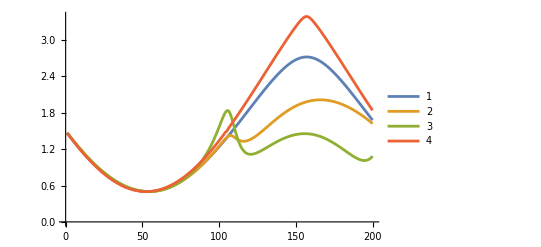

```mathematica
ListPlot[{s1,s2,s3,s4},Joined->True,PlotLegends->Automatic]
```

```mathematica
s1/(3/2)
s2/(3/2)
s3/(3/2)
s4/(3/2)
```

{0.977528,0.955319,0.933384,0.911729,0.890364,0.869297,0.848536,0.828089,0.807964,0.788169,0.76871,0.749597,0.730835,0.712433,0.694397,0.676735,0.659453,0.642557,0.626054,0.609951,0.594253,0.578967,0.564098,0.549653,0.535635,0.522051,0.508906,0.496205,0.483953,0.472153,0.460811,0.44993,0.439515,0.42957,0.420097,0.411101,0.402585,0.394552,0.387004,0.379945,0.373376,0.3673,0.361719,0.356635,0.352049,0.347963,0.344378,0.341295,0.338715,0.336638,0.335065,0.333996,0.333431,0.333369,0.333811,0.334755,0.3362,0.338146,0.340591,0.343533,0.346971,0.350903,0.355326,0.360239,0.365639,0.371522,0.377886,0.384727,0.392042,0.399828,0.40808,0.416795,0.425968,0.435594,0.44567,0.456189,0.467147,0.478539,0.490358,0.5026,0.515258,0.528326,0.541797,0.555666,0.569925,0.584567,0.599585,0.614972,0.63072,0.646821,0.663268,0.680051,0.697163,0.714595,0.732337,0.750382,0.768718,0.787338,0.806231,0.825388,0.844797,0.864449,0.884333,0.904437,0.924751,0.945264,0.965962,0.986835,1.00787,1.02905,1.05038,1.07182,1.09337,1.11502,1.13675,1.15855,1.18039,1.20228,1.22418,1.24608,1.26796,1.28982,1.31162,1.33335,1.35498,1.37651,1.3979,1.41913,1.44017,1.46102,1.48162,1.50197,1.52202,1.54176,1.56114,1.58013,1.5987,1.61681,1.63442,1.65148,1.66797,1.68382,1.69899,1.71344,1.7271,1.73995,1.75191,1.76294,1.77299,1.782,1.78994,1.79676,1.80241,1.80687,1.8101,1.81209,1.81282,1.81229,1.8105,1.80747,1.8032,1.79774,1.7911,1.78334,1.77449,1.76461,1.75373,1.74191,1.72921,1.71567,1.70134,1.68628,1.67053,1.65415,1.63717,1.61965,1.60162,1.58312,1.56419,1.54487,1.52519,1.50518,1.48488,1.46431,1.44351,1.42249,1.40129,1.37992,1.35842,1.3368,1.31508,1.29329,1.27145,1.24957,1.22766,1.20576,1.18388,1.16202,1.14022,1.11848}

{0.977729,0.955711,0.933955,0.912471,0.891266,0.87035,0.849731,0.829418,0.809419,0.789742,0.770394,0.751384,0.73272,0.714407,0.696454,0.678868,0.661656,0.644824,0.628379,0.612327,0.596674,0.581427,0.56659,0.55217,0.538173,0.524602,0.511464,0.498764,0.486505,0.474692,0.46333,0.452423,0.441974,0.431987,0.422467,0.413415,0.404835,0.396731,0.389105,0.381959,0.375295,0.369117,0.363426,0.358224,0.353511,0.349291,0.345564,0.342331,0.339594,0.337352,0.335606,0.334357,0.333606,0.333351,0.333593,0.334332,0.335567,0.337299,0.339525,0.342245,0.345459,0.349164,0.353361,0.358047,0.363221,0.368882,0.375027,0.381655,0.388765,0.396353,0.404419,0.412959,0.421973,0.431456,0.441408,0.451825,0.462705,0.474046,0.485845,0.498099,0.510806,0.523962,0.537566,0.551613,0.566101,0.581026,0.596385,0.612173,0.628386,0.64502,0.662067,0.679522,0.697375,0.715617,0.734234,0.753209,0.77252,0.792135,0.812011,0.832085,0.85226,0.872383,0.892196,0.91124,0.928646,0.942735,0.950645,0.949656,0.940842,0.928456,0.915942,0.905044,0.896487,0.890506,0.8871,0.886151,0.887486,0.890901,0.896185,0.903129,0.911529,0.921192,0.931938,0.943601,0.956029,0.969084,0.982639,0.996582,1.01081,1.02523,1.03977,1.05434,1.0689,1.08336,1.09769,1.11184,1.12576,1.13943,1.15279,1.16584,1.17853,1.19084,1.20276,1.21426,1.22532,1.23594,1.24609,1.25577,1.26496,1.27366,1.28185,1.28953,1.29669,1.30334,1.30945,1.31504,1.32009,1.32462,1.3286,1.33206,1.33497,1.33736,1.33921,1.34054,1.34133,1.34161,1.34136,1.34059,1.33931,1.33753,1.33524,1.33245,1.32918,1.32541,1.32117,1.31645,1.31127,1.30563,1.29953,1.293,1.28602,1.27862,1.2708,1.26256,1.25393,1.24489,1.23547,1.22567,1.21551,1.20498,1.19409,1.18286,1.17129,1.15938,1.14713,1.13455,1.12163,1.10834,1.09465,1.0805}

{0.978178,0.956585,0.935232,0.914127,0.893281,0.872703,0.852401,0.832384,0.812662,0.793243,0.774134,0.755345,0.736883,0.718756,0.700972,0.683538,0.66646,0.649747,0.633405,0.617441,0.60186,0.58667,0.571876,0.557484,0.543499,0.529927,0.516774,0.504043,0.491741,0.479871,0.468438,0.457446,0.446899,0.436802,0.427157,0.417968,0.409239,0.400973,0.393172,0.38584,0.378979,0.372592,0.366681,0.361249,0.356297,0.351828,0.347844,0.344347,0.341338,0.33882,0.336794,0.335262,0.334226,0.333688,0.333649,0.334112,0.335079,0.336552,0.338533,0.341025,0.344031,0.347554,0.351598,0.356168,0.361266,0.3669,0.373075,0.379796,0.387073,0.394913,0.403326,0.412323,0.421916,0.43212,0.442951,0.454427,0.466568,0.479398,0.492944,0.507235,0.522306,0.538196,0.554948,0.572611,0.591242,0.610902,0.631662,0.653602,0.676807,0.701373,0.727405,0.755013,0.784314,0.815422,0.848444,0.883464,0.920527,0.959596,1.00051,1.04288,1.08599,1.1285,1.16814,1.20109,1.22155,1.22232,1.19867,1.15305,1.09416,1.03127,0.970945,0.916915,0.870834,0.833061,0.803208,0.780505,0.764031,0.752854,0.7461,0.742993,0.742861,0.745135,0.74934,0.75508,0.762029,0.769916,0.778519,0.787654,0.797167,0.806932,0.816839,0.8268,0.836737,0.846583,0.856281,0.865782,0.875041,0.884021,0.892685,0.901003,0.908946,0.916489,0.923608,0.930281,0.936488,0.942211,0.947432,0.952137,0.95631,0.959939,0.963012,0.965519,0.967449,0.968795,0.969551,0.96971,0.96927,0.968226,0.966579,0.964327,0.961473,0.958019,0.953971,0.949334,0.944117,0.938328,0.931979,0.925084,0.917656,0.909712,0.901272,0.892356,0.882988,0.873193,0.863001,0.852443,0.841555,0.830376,0.818951,0.807328,0.795564,0.783719,0.771866,0.760084,0.748464,0.737111,0.726144,0.715702,0.705942,0.69705,0.689236,0.682747,0.677865,0.674917,0.674275,0.676362,0.681655,0.690681,0.704007,0.72223}

{0.977053,0.954382,0.931996,0.909903,0.888112,0.866633,0.845473,0.824641,0.804145,0.783995,0.764197,0.744759,0.72569,0.706997,0.688687,0.670768,0.653247,0.636131,0.619427,0.603141,0.587281,0.571851,0.556859,0.542311,0.528211,0.514567,0.501383,0.488665,0.476417,0.464645,0.453353,0.442546,0.432228,0.422403,0.413076,0.404249,0.395927,0.388112,0.380809,0.374019,0.367745,0.361991,0.356757,0.352047,0.347862,0.344205,0.341075,0.338475,0.336406,0.334868,0.333862,0.333388,0.333447,0.334039,0.335162,0.336818,0.339005,0.341722,0.344968,0.348743,0.353043,0.357868,0.363216,0.369085,0.375471,0.382373,0.389788,0.397713,0.406145,0.41508,0.424514,0.434444,0.444867,0.455777,0.46717,0.479043,0.491389,0.504205,0.517484,0.531222,0.545413,0.560052,0.575133,0.590649,0.606594,0.622963,0.639748,0.656944,0.674542,0.692537,0.710921,0.729687,0.748829,0.768338,0.788207,0.80843,0.829001,0.849912,0.871161,0.892745,0.914672,0.936967,0.959732,0.983525,0.997187,1.02583,1.05013,1.07415,1.09826,1.12254,1.147,1.17164,1.19647,1.22147,1.24665,1.27198,1.29746,1.32308,1.34884,1.37471,1.4007,1.42678,1.45295,1.4792,1.50551,1.53188,1.5583,1.58475,1.61122,1.6377,1.66418,1.69064,1.71708,1.74348,1.76983,1.79612,1.82232,1.84844,1.87445,1.90034,1.92609,1.95168,1.97709,2.0023,2.02727,2.05199,2.07639,2.10044,2.12404,2.14711,2.16947,2.1909,2.21099,2.2291,2.24414,2.25443,2.25808,2.25421,2.2438,2.22877,2.21074,2.19079,2.16952,2.14733,2.12445,2.10103,2.07716,2.05293,2.02839,2.00358,1.97853,1.95328,1.92784,1.90223,1.87649,1.85061,1.82463,1.79854,1.77238,1.74614,1.71985,1.69352,1.66715,1.64077,1.61438,1.588,1.56163,1.53529,1.509,1.48275,1.45657,1.43046,1.40444,1.37851,1.35269,1.32698,1.30141,1.27597,1.25068,1.22555}

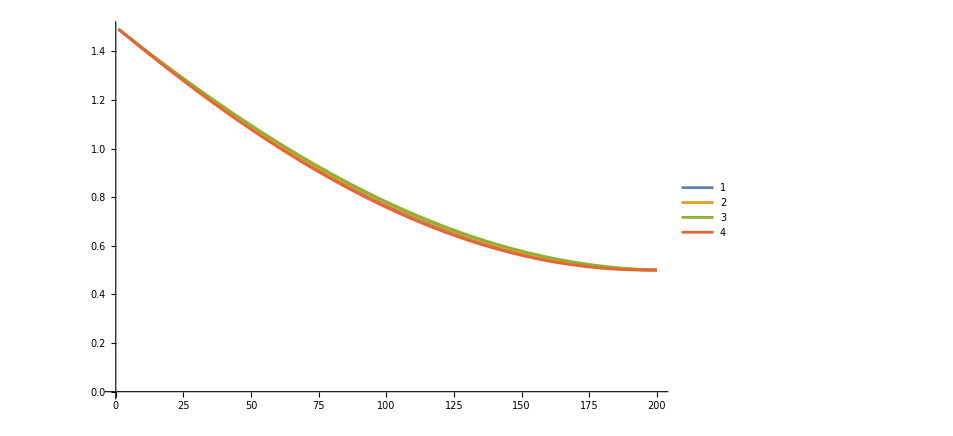

```mathematica
ListPlot[{s1,s2,s3,s4},Joined->True,PlotLegends->Automatic]
```